```mathematica
Clear["Global`*"]
```

#### Fourier Transformation

```mathematica
q=N[Array[((#-1)/100*2π-π)&,101]]
```

{-3.14159,-3.07876,-3.01593,-2.9531,-2.89027,-2.82743,-2.7646,-2.70177,-2.63894,-2.57611,-2.51327,-2.45044,-2.38761,-2.32478,-2.26195,-2.19911,-2.13628,-2.07345,-2.01062,-1.94779,-1.88496,-1.82212,-1.75929,-1.69646,-1.63363,-1.5708,-1.50796,-1.44513,-1.3823,-1.31947,-1.25664,-1.19381,-1.13097,-1.06814,-1.00531,-0.942478,-0.879646,-0.816814,-0.753982,-0.69115,-0.628319,-0.565487,-0.502655,-0.439823,-0.376991,-0.314159,-0.251327,-0.188496,-0.125664,-0.0628319,0.,0.0628319,0.125664,0.188496,0.251327,0.314159,0.376991,0.439823,0.502655,0.565487,0.628319,0.69115,0.753982,0.816814,0.879646,0.942478,1.00531,1.06814,1.13097,1.19381,1.25664,1.31947,1.3823,1.44513,1.50796,1.5708,1.63363,1.69646,1.75929,1.82212,1.88496,1.94779,2.01062,2.07345,2.13628,2.19911,2.26195,2.32478,2.38761,2.45044,2.51327,2.57611,2.63894,2.70177,2.7646,2.82743,2.89027,2.9531,3.01593,3.07876,3.14159}

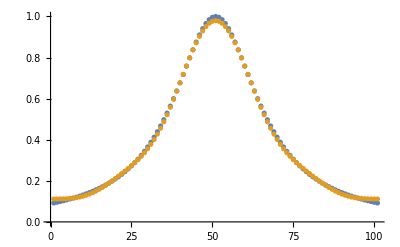

```mathematica
qk=Table[1/101 Sum[Re[1/(q[[i]]^2+1)Exp[ⅈ q[[i]] R]],{i,1,101}],{R,-4,4}];
s=Table[Re[Sum[Re[qk[[R]]Exp[-ⅈ q[[i]] (R-(Length[qk]+1)/2)]],{R,1,Length[qk]}]],{i,1,101}];
ListPlot[{Table[1/(q[[i]]^2+1),{i,1,101}],s},PlotRange->All]
```

```mathematica
qk=Table[1/101 Sum[1/(q[[i]]^2+1)Exp[ⅈ q[[i]] R],{i,1,101}],{R,-5,5}]
s=Table[Re[Sum[qk[[R]]Exp[-ⅈ q[[i]] (R-(Length[qk]+1)/2)],{R,1,Length[qk]}]],{i,1,101}]
```

{0.00307817+1.26284×10^-18 ⅈ,0.00897802+5.04923×10^-18 ⅈ,0.0254478+6.95874×10^-19 ⅈ,0.0643836-2.49062×10^-18 ⅈ,0.191615-1.22804×10^-17 ⅈ,0.398833+0. ⅈ,0.191615+1.22804×10^-17 ⅈ,0.0643836+2.49062×10^-18 ⅈ,0.0254478-6.95874×10^-19 ⅈ,0.00897802-5.04923×10^-18 ⅈ,0.00307817-1.26284×10^-18 ⅈ}

{0.105274,0.105654,0.106779,0.108614,0.1111,0.114167,0.117741,0.121752,0.126142,0.130876,0.135942,0.141357,0.147164,0.153428,0.160232,0.167662,0.175808,0.184745,0.194534,0.205213,0.216801,0.229295,0.242678,0.256932,0.272044,0.288022,0.304902,0.32276,0.341717,0.361935,0.383612,0.406973,0.432244,0.459637,0.489314,0.521367,0.555787,0.592438,0.631044,0.671176,0.712253,0.753551,0.794227,0.833343,0.869914,0.902945,0.931487,0.95468,0.9718,0.982299,0.985838,0.982299,0.9718,0.95468,0.931487,0.902945,0.869914,0.833343,0.794227,0.753551,0.712253,0.671176,0.631044,0.592438,0.555787,0.521367,0.489314,0.459637,0.432244,0.406973,0.383612,0.361935,0.341717,0.32276,0.304902,0.288022,0.272044,0.256932,0.242678,0.229295,0.216801,0.205213,0.194534,0.184745,0.175808,0.167662,0.160232,0.153428,0.147164,0.141357,0.135942,0.130876,0.126142,0.121752,0.117741,0.114167,0.1111,0.108614,0.106779,0.105654,0.105274}

#### Check orthonomal

```mathematica
Clear[Pc,Cc,Dc]
```

```mathematica
ns=1;
fm=Table[{KroneckerDelta[a,b]KroneckerDelta[r,0],KroneckerDelta[a,b]KroneckerDelta[r,-1],KroneckerDelta[a,b]KroneckerDelta[r,1],(1-KroneckerDelta[a,b])KroneckerDelta[r,0]},{a,1,ns},{b,1,ns},{r,-1,1}];
(*fm=Table[{KroneckerDelta[a,b]KroneckerDelta[r,0]},{a,1,ns},{b,1,ns},{r,-1,1}];*)
(*fm (r)a,b,m*)

nf=3;



Pc[R_]:= Evaluate[Array[ToExpression["P"<>ToString[#1]<>ToString[#2]<>ToString[#3]<>ToString[#4]<>ToString[#5]<>ToString[#6]<>"[R]"]&,{ns,ns,nf,ns,ns,nf}]];
Cc[R_] :=Evaluate[ Array[ToExpression["C"<>ToString[#1]<>ToString[#2]<>ToString[#3]<>ToString[#4]<>ToString[#5]<>ToString[#6]<>"[R]"]&,{ns,ns,nf,ns,ns,nf}]];
Dc[R_]:= Evaluate[Array[ToExpression["D"<>ToString[#1]<>ToString[#2]<>ToString[#3]<>ToString[#4]<>ToString[#5]<>ToString[#6]<>"[R]"]&,{ns,ns,nf,ns,ns,nf}]];
```

#### Check

```mathematica
Clear[r,rp]
G=Table[Sum[fm[[a]][[b]][[r]][[m]]Pc[1][[m]][[n]]fm[[c]][[d]][[rp]][[n]],{m,1,4},{n,1,4}]
,{a,1,2},{b,1,2},{c,1,2},{d,1,2},{r,1,3},{rp,1,3}];
Table[Sum[fm[[a]][[b]][[r]][[o]]G[[a]][[b]][[c]][[d]][[r]][[rp]]fm[[c]][[d]][[rp]][[p]],{a,1,2},{b,1,2},{c,1,2},{d,1,2},{r,1,3},{rp,1,3}],{o,1,4},{p,1,4}]//MatrixForm
```

Part::partw: Part 2 of {{{{{P111111[1],P111112[1],P111113[1]}}},{{{P112111[1],P112112[1],P112113[1]}}},{{{P113111[1],P113112[1],P113113[1]}}}}} does not exist.

Part::partw: Part 3 of {{{{{P111111[1],P111112[1],P111113[1]}}},{{{P112111[1],P112112[1],P112113[1]}}},{{{P113111[1],P113112[1],P113113[1]}}}}} does not exist.

Part::partw: Part 4 of {{{{{P111111[1],P111112[1],P111113[1]}}},{{{P112111[1],P112112[1],P112113[1]}}},{{{P113111[1],P113112[1],P113113[1]}}}}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in {{{{0,0,0}}},{{{0,0,0}}},{{{0,0,0}}}}+{{{{{{2,2,2}}},{{{2,2,2}}},{{{2,2,2}}}}}}+{{{{{{0,0,0}}},{{{0,0,0}}},{{{0,0,0}}}}}}+{{{{{{0,0,0}}},{{{0,0,0}}},{{{0,0,0}}}}}} cannot be combined.

Thread::tdlen: Objects of unequal length in {{{{{{0,0,0}}},{{{0,0,0}}},{{{0,0,0}}}}}}+{{{{{{2,2,2}}},{{{2,2,2}}},{{{2,2,2}}}}}}+{{{{0,0,0}}},{{{0,0,0}}},{{{0,0,0}}}} cannot be combined.

Thread::tdlen: Objects of unequal length in {{{{0,0,0}}},{{{0,0,0}}},{{{0,0,0}}}}+{{{{{{P111111[«1»],P111112[«1»],P111113[«1»]}}},{{{P112111[«1»],P112112[«1»],P112113[«1»]}}},{{{P113111[«1»],P113112[«1»],P113113[«1»]}}}}}}+{{{{{{0,0,0}}},{{{0,0,0}}},{{{0,0,0}}}}}}+{{{{{{0,0,0}}},{{{0,0,0}}},{{{0,0,0}}}}}} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Part::partd: Part specification 2⟦1⟧ is longer than depth of object.

Part::partd: Part specification 2⟦2⟧ is longer than depth of object.

Part::partd: Part specification 2⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 2 of {{{0,1,0,0},{1,0,0,0},{0,0,1,0}}} does not exist.

Part::partd: Part specification 2⟦1⟧ is longer than depth of object.

Part::partw: Part 2 of {{{0,1,0,0},{1,0,0,0},{0,0,1,0}}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification 2⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in {{{{{{0,0,0}}},{{{0,0,0}}},{{{0,0,0}}}}}}+{{{{P111111[1],P111112[1],P111113[1]}}},{{{P112111[1],P112112[1],P112113[1]}}},{{{P113111[1],P113112[1],P113113[1]}}}}+{«1»} cannot be combined.

Thread::tdlen: Objects of unequal length in {{0,0,0,0},{0,0,0,0},{0,0,0,0}}+{{{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}}+{{{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}} cannot be combined.

Thread::tdlen: Objects of unequal length in {{{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}}+{{0,0,0,0},{0,0,0,0},{0,0,0,0}} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

(1)
 |  |  |  |

```mathematica
G=Table[Sum[fm[[a]][[c]][[r]][[m]]Cc[{-3,r-2,rp-2}/.C2P][[m]][[n]]fm[[b]][[d]][[rp]][[n]],{m,1,4},{n,1,4}]
,{a,1,2},{b,1,2},{c,1,2},{d,1,2},{r,1,3},{rp,1,3}];
Table[Sum[fm[[a]][[b]][[r]][[o]]G[[a]][[b]][[c]][[d]][[r]][[rp]]fm[[c]][[d]][[rp]][[p]],{a,1,2},{b,1,2},{c,1,2},{d,1,2},{r,1,3},{rp,1,3}],{o,1,4},{p,1,4}]//MatrixForm
```

ReplaceAll::reps: {C2P} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 2 of {{{{{C111111[{«3»}/.C2P],C111112[{«3»}/.C2P],C111113[{«3»}/.C2P]}}},{{{C112111[{«3»}/.C2P],C112112[{«3»}/.C2P],C112113[{«3»}/.C2P]}}},{{{C113111[{«3»}/.C2P],C113112[{«3»}/.C2P],C113113[{«3»}/.C2P]}}}}} does not exist.

ReplaceAll::reps: {C2P} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 3 of {{{{{C111111[{«3»}/.C2P],C111112[{«3»}/.C2P],C111113[{«3»}/.C2P]}}},{{{C112111[{«3»}/.C2P],C112112[{«3»}/.C2P],C112113[{«3»}/.C2P]}}},{{{C113111[{«3»}/.C2P],C113112[{«3»}/.C2P],C113113[{«3»}/.C2P]}}}}} does not exist.

Part::partw: Part 4 of {{{{{C111111[{«3»}/.C2P],C111112[{«3»}/.C2P],C111113[{«3»}/.C2P]}}},{{{C112111[{«3»}/.C2P],C112112[{«3»}/.C2P],C112113[{«3»}/.C2P]}}},{{{C113111[{«3»}/.C2P],C113112[{«3»}/.C2P],C113113[{«3»}/.C2P]}}}}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in {{{{0,0,0}}},{{{0,0,0}}},{{{0,0,0}}}}+{{{{{{2,2,2}}},{{{2,2,2}}},{{{2,2,2}}}}}}+{{{{{{0,0,0}}},{{{0,0,0}}},{{{0,0,0}}}}}}+{{{{{{0,0,0}}},{{{0,0,0}}},{{{0,0,0}}}}}} cannot be combined.

Thread::tdlen: Objects of unequal length in {{{{{{0,0,0}}},{{{0,0,0}}},{{{0,0,0}}}}}}+{{{{{{2,2,2}}},{{{2,2,2}}},{{{2,2,2}}}}}}+{{{{0,0,0}}},{{{0,0,0}}},{{{0,0,0}}}} cannot be combined.

Thread::tdlen: Objects of unequal length in {{{{0,0,0}}},{{{0,0,0}}},{{{0,0,0}}}}+{{{{{{C111111[«1»],C111112[«1»],C111113[«1»]}}},{{{C112111[«1»],C112112[«1»],C112113[«1»]}}},{{{C113111[«1»],C113112[«1»],C113113[«1»]}}}}}}+{{{{{{0,0,0}}},{{{0,0,0}}},{{{0,0,0}}}}}}+{{{{{{0,0,0}}},{{{0,0,0}}},{{{0,0,0}}}}}} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Part::partd: Part specification 2⟦1⟧ is longer than depth of object.

Part::partd: Part specification 2⟦2⟧ is longer than depth of object.

Part::partd: Part specification 2⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 2 of {{{0,1,0,0},{1,0,0,0},{0,0,1,0}}} does not exist.

Part::partd: Part specification 2⟦1⟧ is longer than depth of object.

Part::partw: Part 2 of {{{0,1,0,0},{1,0,0,0},{0,0,1,0}}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification 2⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in {{{{{{0,0,0}}},{{{0,0,0}}},{{{0,0,0}}}}}}+{{{{C111111[{«3»}/.C2P],C111112[{«3»}/.C2P],C111113[{«3»}/.C2P]}}},{{{C112111[{«3»}/.C2P],C112112[{«3»}/.C2P],C112113[{«3»}/.C2P]}}},{{{C113111[{«3»}/.C2P],C113112[{«3»}/.C2P],C113113[{«3»}/.C2P]}}}}+{«1»} cannot be combined.

Thread::tdlen: Objects of unequal length in {{0,0,0,0},{0,0,0,0},{0,0,0,0}}+{{{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}}+{{{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}} cannot be combined.

Thread::tdlen: Objects of unequal length in {{{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}}+{{0,0,0,0},{0,0,0,0},{0,0,0,0}} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

(1)
 |  |  |  |

```mathematica
G=Table[Sum[fm[[a]][[d]][[r]][[m]]Dc[{-1,r-2,rp-2}/.D2P][[m]][[n]]fm[[b]][[c]][[rp]][[n]],{m,1,4},{n,1,4}]
,{a,1,2},{b,1,2},{c,1,2},{d,1,2},{r,1,3},{rp,1,3}];
Table[Sum[fm[[a]][[b]][[r]][[o]]G[[a]][[b]][[c]][[d]][[r]][[rp]]fm[[c]][[d]][[rp]][[p]],{a,1,2},{b,1,2},{c,1,2},{d,1,2},{r,1,3},{rp,1,3}],{o,1,4},{p,1,4}]//MatrixForm
```

ReplaceAll::reps: {D2P} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 2 of {{{{{D111111[{«3»}/.D2P],D111112[{«3»}/.D2P],D111113[{«3»}/.D2P]}}},{{{D112111[{«3»}/.D2P],D112112[{«3»}/.D2P],D112113[{«3»}/.D2P]}}},{{{D113111[{«3»}/.D2P],D113112[{«3»}/.D2P],D113113[{«3»}/.D2P]}}}}} does not exist.

ReplaceAll::reps: {D2P} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 3 of {{{{{D111111[{«3»}/.D2P],D111112[{«3»}/.D2P],D111113[{«3»}/.D2P]}}},{{{D112111[{«3»}/.D2P],D112112[{«3»}/.D2P],D112113[{«3»}/.D2P]}}},{{{D113111[{«3»}/.D2P],D113112[{«3»}/.D2P],D113113[{«3»}/.D2P]}}}}} does not exist.

Part::partw: Part 4 of {{{{{D111111[{«3»}/.D2P],D111112[{«3»}/.D2P],D111113[{«3»}/.D2P]}}},{{{D112111[{«3»}/.D2P],D112112[{«3»}/.D2P],D112113[{«3»}/.D2P]}}},{{{D113111[{«3»}/.D2P],D113112[{«3»}/.D2P],D113113[{«3»}/.D2P]}}}}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in {{{{0,0,0}}},{{{0,0,0}}},{{{0,0,0}}}}+{{{{{{2,2,2}}},{{{2,2,2}}},{{{2,2,2}}}}}}+{{{{{{0,0,0}}},{{{0,0,0}}},{{{0,0,0}}}}}}+{{{{{{0,0,0}}},{{{0,0,0}}},{{{0,0,0}}}}}} cannot be combined.

Thread::tdlen: Objects of unequal length in {{{{{{0,0,0}}},{{{0,0,0}}},{{{0,0,0}}}}}}+{{{{{{2,2,2}}},{{{2,2,2}}},{{{2,2,2}}}}}}+{{{{0,0,0}}},{{{0,0,0}}},{{{0,0,0}}}} cannot be combined.

Thread::tdlen: Objects of unequal length in {{{{0,0,0}}},{{{0,0,0}}},{{{0,0,0}}}}+{{{{{{D111111[«1»],D111112[«1»],D111113[«1»]}}},{{{D112111[«1»],D112112[«1»],D112113[«1»]}}},{{{D113111[«1»],D113112[«1»],D113113[«1»]}}}}}}+{{{{{{0,0,0}}},{{{0,0,0}}},{{{0,0,0}}}}}}+{{{{{{0,0,0}}},{{{0,0,0}}},{{{0,0,0}}}}}} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Part::partd: Part specification 2⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 2 of {{{0,1,0,0},{1,0,0,0},{0,0,1,0}}} does not exist.

Part::partd: Part specification 2⟦1⟧ is longer than depth of object.

Part::partw: Part 2 of {{{0,1,0,0},{1,0,0,0},{0,0,1,0}}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification 2⟦1⟧ is longer than depth of object.

Thread::tdlen: Objects of unequal length in … cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Part::partd: Part specification 2⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

(1)
 |  |  |  |

#### Mapping !!!!!!!!!!

```mathematica
P2C={};
C2P={};
P2D={};
D2P={};
C2D={};
D2C={};
cut=10^-3;
Do[
{
If[Abs[Rc+dc-rp]<cut && Abs[Rc-Rp]<cut && Abs[Rp+dp-rc]<cut,
{AppendTo[P2C,{Rp,rp,dp}-> Rc],
AppendTo[C2P,{Rc,rc,dc}-> Rp]}]
},

{Rp,-6,6},{rp,-1,1},{dp,-1,1},{Rc,-6,6},{rc,-1,1},{dc,-1,1}]

Do[
{
If[Abs[Rd+dd-rp]<cut && Abs[rd-Rp]<cut && Abs[Rp+dp-Rd]<cut,
{AppendTo[P2D,{Rp,rp,dp}->Rd],
AppendTo[D2P,{Rd,rd,dd}->Rp]}]
},

{Rp,-6,6},{rp,-1,1},{dp,-1,1},{Rd,-6,6},{rd,-1,1},{dd,-1,1}]

Do[
{
If[Abs[Rd+dd-Rc-dc]<cut && Abs[rd-Rc]<cut && Abs[rc-Rd]<cut,
{AppendTo[C2D,{Rc,rc,dc}-> Rd],
AppendTo[D2C,{Rd,rd,dd}-> Rc]}]
},

{Rc,-6,6},{rc,-1,1},{dc,-1,1},{Rd,-6,6},{rd,-1,1},{dd,-1,1}]
```

Rules

```mathematica
Clear[ss]
```

#### rule

```mathematica
rule =Flatten[Table[ToExpression["C"<>ToString[a]<>ToString[b]<>ToString[m]<>ToString[c]<>ToString[d]<>ToString[n]<>"[i_]"]->dCchanRs[i+ss,a-1,b-1,m-1,c-1,d-1,n-1],{a,1,ns},{b,1,ns},{m,1,nf},{c,1,ns},{d,1,ns},{n,1,nf}]];
AppendTo[rule,Flatten[Table[ToExpression["P"<>ToString[a]<>ToString[b]<>ToString[m]<>ToString[c]<>ToString[d]<>ToString[n]<>"[i_]"]->dPchanRs[i+ss,a-1,b-1,m-1,c-1,d-1,n-1],{a,1,ns},{b,1,ns},{m,1,nf},{c,1,ns},{d,1,ns},{n,1,nf}]]];
AppendTo[rule,Flatten[Table[ToExpression["D"<>ToString[a]<>ToString[b]<>ToString[m]<>ToString[c]<>ToString[d]<>ToString[n]<>"[i_]"]->dDchanRs[i+ss,a-1,b-1,m-1,c-1,d-1,n-1],{a,1,ns},{b,1,ns},{m,1,nf},{c,1,ns},{d,1,ns},{n,1,nf}]]];
rule = Flatten[rule]
```

{C111111[i_]→dCchanRs[i+ss,0,0,0,0,0,0],C111112[i_]→dCchanRs[i+ss,0,0,0,0,0,1],C111113[i_]→dCchanRs[i+ss,0,0,0,0,0,2],C112111[i_]→dCchanRs[i+ss,0,0,1,0,0,0],C112112[i_]→dCchanRs[i+ss,0,0,1,0,0,1],C112113[i_]→dCchanRs[i+ss,0,0,1,0,0,2],C113111[i_]→dCchanRs[i+ss,0,0,2,0,0,0],C113112[i_]→dCchanRs[i+ss,0,0,2,0,0,1],C113113[i_]→dCchanRs[i+ss,0,0,2,0,0,2],P111111[i_]→dPchanRs[i+ss,0,0,0,0,0,0],P111112[i_]→dPchanRs[i+ss,0,0,0,0,0,1],P111113[i_]→dPchanRs[i+ss,0,0,0,0,0,2],P112111[i_]→dPchanRs[i+ss,0,0,1,0,0,0],P112112[i_]→dPchanRs[i+ss,0,0,1,0,0,1],P112113[i_]→dPchanRs[i+ss,0,0,1,0,0,2],P113111[i_]→dPchanRs[i+ss,0,0,2,0,0,0],P113112[i_]→dPchanRs[i+ss,0,0,2,0,0,1],P113113[i_]→dPchanRs[i+ss,0,0,2,0,0,2],D111111[i_]→dDchanRs[i+ss,0,0,0,0,0,0],D111112[i_]→dDchanRs[i+ss,0,0,0,0,0,1],D111113[i_]→dDchanRs[i+ss,0,0,0,0,0,2],D112111[i_]→dDchanRs[i+ss,0,0,1,0,0,0],D112112[i_]→dDchanRs[i+ss,0,0,1,0,0,1],D112113[i_]→dDchanRs[i+ss,0,0,1,0,0,2],D113111[i_]→dDchanRs[i+ss,0,0,2,0,0,0],D113112[i_]→dDchanRs[i+ss,0,0,2,0,0,1],D113113[i_]→dDchanRs[i+ss,0,0,2,0,0,2]}

#### Mixed channel

```mathematica
ee="\t"<>"nR2 = int((nR-1)/2)"<>"\n";
Do[{
G=Table[Sum[
fm[[a]][[b]][[r]][[m]]Pc[Ri][[a]][[b]][[m]][[c]][[d]][[n]]fm[[c]][[d]][[rp]][[n]]+fm[[a]][[c]][[r]][[m]]Cc[{Ri,r-2,rp-2}/.C2P][[a]][[c]][[m]][[b]][[d]][[n]]fm[[b]][[d]][[rp]][[n]]+
fm[[a]][[d]][[r]][[m]]Dc[{Ri,r-2,rp-2}/.D2P][[a]][[d]][[m]][[b]][[c]][[n]]fm[[b]][[c]][[rp]][[n]]
,{m,1,nf},{n,1,nf}]
,{a,1,ns},{b,1,ns},{c,1,ns},{d,1,ns},{r,1,3},{rp,1,3}];
PP=Table[Sum[fm[[a]][[b]][[r]][[o]]G[[a]][[b]][[c]][[d]][[r]][[rp]]fm[[c]][[d]][[rp]][[p]],{r,1,3},{rp,1,3}],{a,1,ns},{b,1,ns},{o,1,nf},{c,1,ns},{d,1,ns},{p,1,nf}];
Do[PP[[a]][[b]][[o]][[c]][[d]][[p]]=Evaluate[PP[[a]][[b]][[o]][[c]][[d]][[p]]/.{D_[List[a_,b_,c_]]-> 0}],{a,1,ns},{b,1,ns},{o,1,nf},{c,1,ns},{d,1,ns},{p,1,nf}];
sp=PP/.rule;
e1="\t"<>"cfg.dPchanRQ[R + nR2] = "<>StringReplace[ToString[sp,InputForm],{"{"->"[","}"->"]"}]<>"\n";
(*#######################################################################################*)
G=Table[Sum[
fm[[a]][[c]][[r]][[m]]Cc[Ri][[a]][[c]][[m]][[b]][[d]][[n]]fm[[b]][[d]][[rp]][[n]]+fm[[a]][[b]][[r]][[m]]Pc[{Ri,r-2,rp-2}/.P2C][[a]][[b]][[m]][[c]][[d]][[n]]fm[[c]][[d]][[rp]][[n]]+
fm[[a]][[d]][[r]][[m]]Dc[{Ri,r-2,rp-2}/.D2C][[a]][[d]][[m]][[b]][[c]][[n]]fm[[b]][[c]][[rp]][[n]]
,{m,1,nf},{n,1,nf}]
,{a,1,ns},{b,1,ns},{c,1,ns},{d,1,ns},{r,1,3},{rp,1,3}];
PP=Table[Sum[fm[[a]][[c]][[r]][[o]]G[[a]][[b]][[c]][[d]][[r]][[rp]]fm[[b]][[d]][[rp]][[p]],{r,1,3},{rp,1,3}],{a,1,ns},{b,1,ns},{o,1,nf},{c,1,ns},{d,1,ns},{p,1,nf}];
Do[PP[[a]][[b]][[o]][[c]][[d]][[p]]=Evaluate[PP[[a]][[b]][[o]][[c]][[d]][[p]]/.{D_[List[a_,b_,c_]]-> 0}],{a,1,ns},{b,1,ns},{o,1,nf},{c,1,ns},{d,1,ns},{p,1,nf}];
sp=PP/.rule;
e2="\t"<>"cfg.dCchanRQ[R + nR2] = "<>StringReplace[ToString[sp,InputForm],{"{"->"[","}"->"]"}]<>"\n";
(*#######################################################################################*)
G=Table[Sum[
fm[[a]][[d]][[r]][[m]]Dc[Ri][[a]][[d]][[m]][[b]][[c]][[n]]fm[[b]][[c]][[rp]][[n]]+fm[[a]][[b]][[r]][[m]]Pc[{Ri,r-2,rp-2}/.P2D][[a]][[b]][[m]][[c]][[d]][[n]]fm[[c]][[d]][[rp]][[n]]+
fm[[a]][[c]][[r]][[m]]Cc[{Ri,r-2,rp-2}/.C2D][[a]][[c]][[m]][[b]][[d]][[n]]fm[[b]][[d]][[rp]][[n]]
,{m,1,nf},{n,1,nf}]
,{a,1,ns},{b,1,ns},{c,1,ns},{d,1,ns},{r,1,3},{rp,1,3}];
PP=Table[Sum[fm[[a]][[d]][[r]][[o]]G[[a]][[b]][[c]][[d]][[r]][[rp]]fm[[b]][[c]][[rp]][[p]],{r,1,3},{rp,1,3}],{a,1,ns},{b,1,ns},{o,1,nf},{c,1,ns},{d,1,ns},{p,1,nf}];
Do[PP[[a]][[b]][[o]][[c]][[d]][[p]]=Evaluate[PP[[a]][[b]][[o]][[c]][[d]][[p]]/.{D_[List[a_,b_,c_]]-> 0}],{a,1,ns},{b,1,ns},{o,1,nf},{c,1,ns},{d,1,ns},{p,1,nf}];
sp=PP/.rule;
e3="\t"<>"cfg.dDchanRQ[R + nR2] = "<>StringReplace[ToString[sp,InputForm],{"{"->"[","}"->"]"}]<>"\n";ee=ee<>"\t"<>"R = "<>ToString[Ri]<>"\n"<>e1<>e2<>e3;
ee=StringReplace[ee,"ss"->"nR2"]

}

,{Ri,-2,2}]

ee
```

nR2 = int((nR-1)/2)
	R = -2
	cfg.dPchanRQ[R + nR2] = [[[[[[dPchanRs[-2 + nR2, 0, 0, 0, 0, 0, 0], dPchanRs[-2 + nR2, 0, 0, 0, 0, 0, 1], dPchanRs[-2 + nR2, 0, 0, 0, 0, 0, 2]]]], [[[dPchanRs[-2 + nR2, 0, 0, 1, 0, 0, 0], dPchanRs[-2 + nR2, 0, 0, 1, 0, 0, 1], dCchanRs[-2 + nR2, 0, 0, 1, 0, 0, 2] + dDchanRs[-1 + nR2, 0, 0, 1, 0, 0, 2] + dPchanRs[-2 + nR2, 0, 0, 1, 0, 0, 2]]]], [[[dPchanRs[-2 + nR2, 0, 0, 2, 0, 0, 0], dPchanRs[-2 + nR2, 0, 0, 2, 0, 0, 1], dPchanRs[-2 + nR2, 0, 0, 2, 0, 0, 2]]]]]]]
	cfg.dCchanRQ[R + nR2] = [[[[[[dCchanRs[-2 + nR2, 0, 0, 0, 0, 0, 0], dCchanRs[-2 + nR2, 0, 0, 0, 0, 0, 1], dCchanRs[-2 + nR2, 0, 0, 0, 0, 0, 2]]]], [[[dCchanRs[-2 + nR2, 0, 0, 1, 0, 0, 0], dCchanRs[-2 + nR2, 0, 0, 1, 0, 0, 1], dCchanRs[-2 + nR2, 0, 0, 1, 0, 0, 2] + dPchanRs[-2 + nR2, 0, 0, 1, 0, 0, 2]]]], [[[dCchanRs[-2 + nR2, 0, 0, 2, 0, 0, 0], dCchanRs[-2 + nR2, 0, 0, 2, 0, 0, 1], dCchanRs[-2 + nR2, 0, 0, 2, 0, 0, 2]]]]]]]
	cfg.dDchanRQ[R + nR2] = [[[[[[dDchanRs[-2 + nR2, 0, 0, 0, 0, 0, 0], dDchanRs[-2 + nR2, 0, 0, 0, 0, 0, 1], dDchanRs[-2 + nR2, 0, 0, 0, 0, 0, 2]]]], [[[dDchanRs[-2 + nR2, 0, 0, 1, 0, 0, 0], dDchanRs[-2 + nR2, 0, 0, 1, 0, 0, 1], dDchanRs[-2 + nR2, 0, 0, 1, 0, 0, 2]]]], [[[dDchanRs[-2 + nR2, 0, 0, 2, 0, 0, 0], dDchanRs[-2 + nR2, 0, 0, 2, 0, 0, 1], dDchanRs[-2 + nR2, 0, 0, 2, 0, 0, 2]]]]]]]
	R = -1
	cfg.dPchanRQ[R + nR2] = [[[[[[dCchanRs[-1 + nR2, 0, 0, 0, 0, 0, 0] + dDchanRs[nR2, 0, 0, 0, 0, 0, 0] + dPchanRs[-1 + nR2, 0, 0, 0, 0, 0, 0], dPchanRs[-1 + nR2, 0, 0, 0, 0, 0, 1], dCchanRs[-1 + nR2, 0, 0, 0, 0, 0, 2] + dDchanRs[nR2, 0, 0, 0, 0, 0, 2] + dPchanRs[-1 + nR2, 0, 0, 0, 0, 0, 2]]]], [[[dCchanRs[-1 + nR2, 0, 0, 1, 0, 0, 0] + dDchanRs[-1 + nR2, 0, 0, 1, 0, 0, 0] + dPchanRs[-1 + nR2, 0, 0, 1, 0, 0, 0], dPchanRs[-1 + nR2, 0, 0, 1, 0, 0, 1], dCchanRs[-1 + nR2, 0, 0, 1, 0, 0, 2] + dDchanRs[-1 + nR2, 0, 0, 1, 0, 0, 2] + dPchanRs[-1 + nR2, 0, 0, 1, 0, 0, 2]]]], [[[dPchanRs[-1 + nR2, 0, 0, 2, 0, 0, 0], dPchanRs[-1 + nR2, 0, 0, 2, 0, 0, 1], dPchanRs[-1 + nR2, 0, 0, 2, 0, 0, 2]]]]]]]
	cfg.dCchanRQ[R + nR2] = [[[[[[dCchanRs[-1 + nR2, 0, 0, 0, 0, 0, 0] + dDchanRs[nR2, 0, 0, 0, 0, 0, 0] + dPchanRs[-1 + nR2, 0, 0, 0, 0, 0, 0], dCchanRs[-1 + nR2, 0, 0, 0, 0, 0, 1], dCchanRs[-1 + nR2, 0, 0, 0, 0, 0, 2] + dDchanRs[nR2, 0, 0, 0, 0, 0, 2] + dPchanRs[-1 + nR2, 0, 0, 0, 0, 0, 2]]]], [[[dCchanRs[-1 + nR2, 0, 0, 1, 0, 0, 0] + dDchanRs[-1 + nR2, 0, 0, 1, 0, 0, 0] + dPchanRs[-1 + nR2, 0, 0, 1, 0, 0, 0], dCchanRs[-1 + nR2, 0, 0, 1, 0, 0, 1] + dDchanRs[-1 + nR2, 0, 0, 1, 0, 0, 1], dCchanRs[-1 + nR2, 0, 0, 1, 0, 0, 2] + dDchanRs[-1 + nR2, 0, 0, 1, 0, 0, 2] + dPchanRs[-1 + nR2, 0, 0, 1, 0, 0, 2]]]], [[[dCchanRs[-1 + nR2, 0, 0, 2, 0, 0, 0], dCchanRs[-1 + nR2, 0, 0, 2, 0, 0, 1], dCchanRs[-1 + nR2, 0, 0, 2, 0, 0, 2] + dDchanRs[1 + nR2, 0, 0, 2, 0, 0, 2]]]]]]]
	cfg.dDchanRQ[R + nR2] = [[[[[[dCchanRs[nR2, 0, 0, 0, 0, 0, 0] + dDchanRs[-1 + nR2, 0, 0, 0, 0, 0, 0] + dPchanRs[-1 + nR2, 0, 0, 0, 0, 0, 0], dDchanRs[-1 + nR2, 0, 0, 0, 0, 0, 1], dCchanRs[nR2, 0, 0, 0, 0, 0, 2] + dDchanRs[-1 + nR2, 0, 0, 0, 0, 0, 2] + dPchanRs[nR2, 0, 0, 0, 0, 0, 2]]]], [[[dCchanRs[-1 + nR2, 0, 0, 1, 0, 0, 0] + dDchanRs[-1 + nR2, 0, 0, 1, 0, 0, 0] + dPchanRs[-1 + nR2, 0, 0, 1, 0, 0, 0], dCchanRs[-1 + nR2, 0, 0, 1, 0, 0, 1] + dDchanRs[-1 + nR2, 0, 0, 1, 0, 0, 1] + dPchanRs[-2 + nR2, 0, 0, 1, 0, 0, 1], dCchanRs[-1 + nR2, 0, 0, 1, 0, 0, 2] + dDchanRs[-1 + nR2, 0, 0, 1, 0, 0, 2] + dPchanRs[nR2, 0, 0, 1, 0, 0, 2]]]], [[[dDchanRs[-1 + nR2, 0, 0, 2, 0, 0, 0], dDchanRs[-1 + nR2, 0, 0, 2, 0, 0, 1], dCchanRs[1 + nR2, 0, 0, 2, 0, 0, 2] + dDchanRs[-1 + nR2, 0, 0, 2, 0, 0, 2] + dPchanRs[nR2, 0, 0, 2, 0, 0, 2]]]]]]]
	R = 0
	cfg.dPchanRQ[R + nR2] = [[[[[[dCchanRs[nR2, 0, 0, 0, 0, 0, 0] + dDchanRs[nR2, 0, 0, 0, 0, 0, 0] + dPchanRs[nR2, 0, 0, 0, 0, 0, 0], dCchanRs[nR2, 0, 0, 0, 0, 0, 1] + dDchanRs[nR2, 0, 0, 0, 0, 0, 1] + dPchanRs[nR2, 0, 0, 0, 0, 0, 1], dCchanRs[nR2, 0, 0, 0, 0, 0, 2] + dDchanRs[nR2, 0, 0, 0, 0, 0, 2] + dPchanRs[nR2, 0, 0, 0, 0, 0, 2]]]], [[[dCchanRs[nR2, 0, 0, 1, 0, 0, 0] + dDchanRs[-1 + nR2, 0, 0, 1, 0, 0, 0] + dPchanRs[nR2, 0, 0, 1, 0, 0, 0], dCchanRs[nR2, 0, 0, 1, 0, 0, 1] + dDchanRs[-1 + nR2, 0, 0, 1, 0, 0, 1] + dPchanRs[nR2, 0, 0, 1, 0, 0, 1], dCchanRs[nR2, 0, 0, 1, 0, 0, 2] + dDchanRs[-1 + nR2, 0, 0, 1, 0, 0, 2] + dPchanRs[nR2, 0, 0, 1, 0, 0, 2]]]], [[[dCchanRs[nR2, 0, 0, 2, 0, 0, 0] + dDchanRs[1 + nR2, 0, 0, 2, 0, 0, 0] + dPchanRs[nR2, 0, 0, 2, 0, 0, 0], dCchanRs[nR2, 0, 0, 2, 0, 0, 1] + dDchanRs[1 + nR2, 0, 0, 2, 0, 0, 1] + dPchanRs[nR2, 0, 0, 2, 0, 0, 1], dCchanRs[nR2, 0, 0, 2, 0, 0, 2] + dDchanRs[1 + nR2, 0, 0, 2, 0, 0, 2] + dPchanRs[nR2, 0, 0, 2, 0, 0, 2]]]]]]]
	cfg.dCchanRQ[R + nR2] = [[[[[[dCchanRs[nR2, 0, 0, 0, 0, 0, 0] + dDchanRs[nR2, 0, 0, 0, 0, 0, 0] + dPchanRs[nR2, 0, 0, 0, 0, 0, 0], dCchanRs[nR2, 0, 0, 0, 0, 0, 1] + dDchanRs[nR2, 0, 0, 0, 0, 0, 1] + dPchanRs[nR2, 0, 0, 0, 0, 0, 1], dCchanRs[nR2, 0, 0, 0, 0, 0, 2] + dDchanRs[nR2, 0, 0, 0, 0, 0, 2] + dPchanRs[nR2, 0, 0, 0, 0, 0, 2]]]], [[[dCchanRs[nR2, 0, 0, 1, 0, 0, 0] + dDchanRs[-1 + nR2, 0, 0, 1, 0, 0, 0] + dPchanRs[nR2, 0, 0, 1, 0, 0, 0], dCchanRs[nR2, 0, 0, 1, 0, 0, 1] + dDchanRs[-1 + nR2, 0, 0, 1, 0, 0, 1] + dPchanRs[nR2, 0, 0, 1, 0, 0, 1], dCchanRs[nR2, 0, 0, 1, 0, 0, 2] + dPchanRs[nR2, 0, 0, 1, 0, 0, 2]]]], [[[dCchanRs[nR2, 0, 0, 2, 0, 0, 0] + dDchanRs[1 + nR2, 0, 0, 2, 0, 0, 0] + dPchanRs[nR2, 0, 0, 2, 0, 0, 0], dCchanRs[nR2, 0, 0, 2, 0, 0, 1] + dPchanRs[nR2, 0, 0, 2, 0, 0, 1], dCchanRs[nR2, 0, 0, 2, 0, 0, 2] + dDchanRs[1 + nR2, 0, 0, 2, 0, 0, 2] + dPchanRs[nR2, 0, 0, 2, 0, 0, 2]]]]]]]
	cfg.dDchanRQ[R + nR2] = [[[[[[dCchanRs[nR2, 0, 0, 0, 0, 0, 0] + dDchanRs[nR2, 0, 0, 0, 0, 0, 0] + dPchanRs[nR2, 0, 0, 0, 0, 0, 0], dCchanRs[nR2, 0, 0, 0, 0, 0, 1] + dDchanRs[nR2, 0, 0, 0, 0, 0, 1] + dPchanRs[-1 + nR2, 0, 0, 0, 0, 0, 1], dCchanRs[nR2, 0, 0, 0, 0, 0, 2] + dDchanRs[nR2, 0, 0, 0, 0, 0, 2] + dPchanRs[1 + nR2, 0, 0, 0, 0, 0, 2]]]], [[[dCchanRs[-1 + nR2, 0, 0, 1, 0, 0, 0] + dDchanRs[nR2, 0, 0, 1, 0, 0, 0] + dPchanRs[nR2, 0, 0, 1, 0, 0, 0], dCchanRs[-1 + nR2, 0, 0, 1, 0, 0, 1] + dDchanRs[nR2, 0, 0, 1, 0, 0, 1] + dPchanRs[-1 + nR2, 0, 0, 1, 0, 0, 1], dDchanRs[nR2, 0, 0, 1, 0, 0, 2]]]], [[[dCchanRs[1 + nR2, 0, 0, 2, 0, 0, 0] + dDchanRs[nR2, 0, 0, 2, 0, 0, 0] + dPchanRs[nR2, 0, 0, 2, 0, 0, 0], dDchanRs[nR2, 0, 0, 2, 0, 0, 1], dCchanRs[1 + nR2, 0, 0, 2, 0, 0, 2] + dDchanRs[nR2, 0, 0, 2, 0, 0, 2] + dPchanRs[1 + nR2, 0, 0, 2, 0, 0, 2]]]]]]]
	R = 1
	cfg.dPchanRQ[R + nR2] = [[[[[[dCchanRs[1 + nR2, 0, 0, 0, 0, 0, 0] + dDchanRs[nR2, 0, 0, 0, 0, 0, 0] + dPchanRs[1 + nR2, 0, 0, 0, 0, 0, 0], dCchanRs[1 + nR2, 0, 0, 0, 0, 0, 1] + dDchanRs[nR2, 0, 0, 0, 0, 0, 1] + dPchanRs[1 + nR2, 0, 0, 0, 0, 0, 1], dPchanRs[1 + nR2, 0, 0, 0, 0, 0, 2]]]], [[[dPchanRs[1 + nR2, 0, 0, 1, 0, 0, 0], dPchanRs[1 + nR2, 0, 0, 1, 0, 0, 1], dPchanRs[1 + nR2, 0, 0, 1, 0, 0, 2]]]], [[[dCchanRs[1 + nR2, 0, 0, 2, 0, 0, 0] + dDchanRs[1 + nR2, 0, 0, 2, 0, 0, 0] + dPchanRs[1 + nR2, 0, 0, 2, 0, 0, 0], dCchanRs[1 + nR2, 0, 0, 2, 0, 0, 1] + dDchanRs[1 + nR2, 0, 0, 2, 0, 0, 1] + dPchanRs[1 + nR2, 0, 0, 2, 0, 0, 1], dPchanRs[1 + nR2, 0, 0, 2, 0, 0, 2]]]]]]]
	cfg.dCchanRQ[R + nR2] = [[[[[[dCchanRs[1 + nR2, 0, 0, 0, 0, 0, 0] + dDchanRs[nR2, 0, 0, 0, 0, 0, 0] + dPchanRs[1 + nR2, 0, 0, 0, 0, 0, 0], dCchanRs[1 + nR2, 0, 0, 0, 0, 0, 1] + dDchanRs[nR2, 0, 0, 0, 0, 0, 1] + dPchanRs[1 + nR2, 0, 0, 0, 0, 0, 1], dCchanRs[1 + nR2, 0, 0, 0, 0, 0, 2]]]], [[[dCchanRs[1 + nR2, 0, 0, 1, 0, 0, 0], dCchanRs[1 + nR2, 0, 0, 1, 0, 0, 1] + dDchanRs[-1 + nR2, 0, 0, 1, 0, 0, 1], dCchanRs[1 + nR2, 0, 0, 1, 0, 0, 2]]]], [[[dCchanRs[1 + nR2, 0, 0, 2, 0, 0, 0] + dDchanRs[1 + nR2, 0, 0, 2, 0, 0, 0] + dPchanRs[1 + nR2, 0, 0, 2, 0, 0, 0], dCchanRs[1 + nR2, 0, 0, 2, 0, 0, 1] + dDchanRs[1 + nR2, 0, 0, 2, 0, 0, 1] + dPchanRs[1 + nR2, 0, 0, 2, 0, 0, 1], dCchanRs[1 + nR2, 0, 0, 2, 0, 0, 2] + dDchanRs[1 + nR2, 0, 0, 2, 0, 0, 2]]]]]]]
	cfg.dDchanRQ[R + nR2] = [[[[[[dCchanRs[nR2, 0, 0, 0, 0, 0, 0] + dDchanRs[1 + nR2, 0, 0, 0, 0, 0, 0] + dPchanRs[1 + nR2, 0, 0, 0, 0, 0, 0], dCchanRs[nR2, 0, 0, 0, 0, 0, 1] + dDchanRs[1 + nR2, 0, 0, 0, 0, 0, 1] + dPchanRs[nR2, 0, 0, 0, 0, 0, 1], dDchanRs[1 + nR2, 0, 0, 0, 0, 0, 2]]]], [[[dDchanRs[1 + nR2, 0, 0, 1, 0, 0, 0], dCchanRs[-1 + nR2, 0, 0, 1, 0, 0, 1] + dDchanRs[1 + nR2, 0, 0, 1, 0, 0, 1] + dPchanRs[nR2, 0, 0, 1, 0, 0, 1], dDchanRs[1 + nR2, 0, 0, 1, 0, 0, 2]]]], [[[dCchanRs[1 + nR2, 0, 0, 2, 0, 0, 0] + dDchanRs[1 + nR2, 0, 0, 2, 0, 0, 0] + dPchanRs[1 + nR2, 0, 0, 2, 0, 0, 0], dCchanRs[1 + nR2, 0, 0, 2, 0, 0, 1] + dDchanRs[1 + nR2, 0, 0, 2, 0, 0, 1] + dPchanRs[nR2, 0, 0, 2, 0, 0, 1], dCchanRs[1 + nR2, 0, 0, 2, 0, 0, 2] + dDchanRs[1 + nR2, 0, 0, 2, 0, 0, 2] + dPchanRs[2 + nR2, 0, 0, 2, 0, 0, 2]]]]]]]
	R = 2
	cfg.dPchanRQ[R + nR2] = [[[[[[dPchanRs[2 + nR2, 0, 0, 0, 0, 0, 0], dPchanRs[2 + nR2, 0, 0, 0, 0, 0, 1], dPchanRs[2 + nR2, 0, 0, 0, 0, 0, 2]]]], [[[dPchanRs[2 + nR2, 0, 0, 1, 0, 0, 0], dPchanRs[2 + nR2, 0, 0, 1, 0, 0, 1], dPchanRs[2 + nR2, 0, 0, 1, 0, 0, 2]]]], [[[dPchanRs[2 + nR2, 0, 0, 2, 0, 0, 0], dCchanRs[2 + nR2, 0, 0, 2, 0, 0, 1] + dDchanRs[1 + nR2, 0, 0, 2, 0, 0, 1] + dPchanRs[2 + nR2, 0, 0, 2, 0, 0, 1], dPchanRs[2 + nR2, 0, 0, 2, 0, 0, 2]]]]]]]
	cfg.dCchanRQ[R + nR2] = [[[[[[dCchanRs[2 + nR2, 0, 0, 0, 0, 0, 0], dCchanRs[2 + nR2, 0, 0, 0, 0, 0, 1], dCchanRs[2 + nR2, 0, 0, 0, 0, 0, 2]]]], [[[dCchanRs[2 + nR2, 0, 0, 1, 0, 0, 0], dCchanRs[2 + nR2, 0, 0, 1, 0, 0, 1], dCchanRs[2 + nR2, 0, 0, 1, 0, 0, 2]]]], [[[dCchanRs[2 + nR2, 0, 0, 2, 0, 0, 0], dCchanRs[2 + nR2, 0, 0, 2, 0, 0, 1] + dPchanRs[2 + nR2, 0, 0, 2, 0, 0, 1], dCchanRs[2 + nR2, 0, 0, 2, 0, 0, 2]]]]]]]
	cfg.dDchanRQ[R + nR2] = [[[[[[dDchanRs[2 + nR2, 0, 0, 0, 0, 0, 0], dDchanRs[2 + nR2, 0, 0, 0, 0, 0, 1], dDchanRs[2 + nR2, 0, 0, 0, 0, 0, 2]]]], [[[dDchanRs[2 + nR2, 0, 0, 1, 0, 0, 0], dDchanRs[2 + nR2, 0, 0, 1, 0, 0, 1], dDchanRs[2 + nR2, 0, 0, 1, 0, 0, 2]]]], [[[dDchanRs[2 + nR2, 0, 0, 2, 0, 0, 0], dDchanRs[2 + nR2, 0, 0, 2, 0, 0, 1], dDchanRs[2 + nR2, 0, 0, 2, 0, 0, 2]]]]]]]

#### Single channel 1

```mathematica
ee="\t"<>"for ii in range(cfg.nR):";
Ri=ii;
G=Table[Sum[
fm[[a]][[b]][[r]][[m]]Pc[Ri][[a]][[b]][[m]][[c]][[d]][[n]]fm[[c]][[d]][[rp]][[n]]
,{m,1,nf},{n,1,nf}]
,{a,1,ns},{b,1,ns},{c,1,ns},{d,1,ns},{r,1,3},{rp,1,3}];
PP=Table[Sum[fm[[a]][[b]][[r]][[o]]G[[a]][[b]][[c]][[d]][[r]][[rp]]fm[[c]][[d]][[rp]][[p]],{r,1,3},{rp,1,3}],{a,1,ns},{b,1,ns},{o,1,nf},{c,1,ns},{d,1,ns},{p,1,nf}];
Do[PP[[a]][[b]][[o]][[c]][[d]][[p]]=Evaluate[PP[[a]][[b]][[o]][[c]][[d]][[p]]/.{D_[List[a_,b_,c_]]-> 0}],{a,1,ns},{b,1,ns},{o,1,nf},{c,1,ns},{d,1,ns},{p,1,nf}];
sp=PP/.rule;
e1="\t\t"<>"dPchanRs[ii] = "<>StringReplace[ToString[sp,InputForm],{"{"->"[","}"->"]"}]<>"\n";
(*#######################################################################################*)
G=Table[Sum[
fm[[a]][[c]][[r]][[m]]Cc[Ri][[a]][[c]][[m]][[b]][[d]][[n]]fm[[b]][[d]][[rp]][[n]]
,{m,1,nf},{n,1,nf}]
,{a,1,ns},{b,1,ns},{c,1,ns},{d,1,ns},{r,1,3},{rp,1,3}];
PP=Table[Sum[fm[[a]][[c]][[r]][[o]]G[[a]][[b]][[c]][[d]][[r]][[rp]]fm[[b]][[d]][[rp]][[p]],{r,1,3},{rp,1,3}],{a,1,ns},{b,1,ns},{o,1,nf},{c,1,ns},{d,1,ns},{p,1,nf}];
Do[PP[[a]][[b]][[o]][[c]][[d]][[p]]=Evaluate[PP[[a]][[b]][[o]][[c]][[d]][[p]]/.{D_[List[a_,b_,c_]]-> 0}],{a,1,ns},{b,1,ns},{o,1,nf},{c,1,ns},{d,1,ns},{p,1,nf}];
sp=PP/.rule;
e2="\t\t"<>"dCchanRs[ii] = "<>StringReplace[ToString[sp,InputForm],{"{"->"[","}"->"]"}]<>"\n";
(*#######################################################################################*)
G=Table[Sum[
fm[[a]][[d]][[r]][[m]]Dc[Ri][[a]][[d]][[m]][[b]][[c]][[n]]fm[[b]][[c]][[rp]][[n]]
,{m,1,nf},{n,1,nf}]
,{a,1,ns},{b,1,ns},{c,1,ns},{d,1,ns},{r,1,3},{rp,1,3}];
PP=Table[Sum[fm[[a]][[d]][[r]][[o]]G[[a]][[b]][[c]][[d]][[r]][[rp]]fm[[b]][[c]][[rp]][[p]],{r,1,3},{rp,1,3}],{a,1,ns},{b,1,ns},{o,1,nf},{c,1,ns},{d,1,ns},{p,1,nf}];
Do[PP[[a]][[b]][[o]][[c]][[d]][[p]]=Evaluate[PP[[a]][[b]][[o]][[c]][[d]][[p]]/.{D_[List[a_,b_,c_]]-> 0}],{a,1,ns},{b,1,ns},{o,1,nf},{c,1,ns},{d,1,ns},{p,1,nf}];
sp=PP/.rule;
e3="\t\t"<>"dDchanRs[ii] = "<>StringReplace[ToString[sp,InputForm],{"{"->"[","}"->"]"}]<>"\n";
ee=ee<>"\n"<>e1<>e2<>e3;
ee=StringReplace[ee," + ss"->""]
```

for ii in range(cfg.nR):
		dPchanRs[ii] = [[[[[[dPchanRs[ii, 0, 0, 0, 0, 0, 0], dPchanRs[ii, 0, 0, 0, 0, 0, 1], dPchanRs[ii, 0, 0, 0, 0, 0, 2]]]], [[[dPchanRs[ii, 0, 0, 1, 0, 0, 0], dPchanRs[ii, 0, 0, 1, 0, 0, 1], dPchanRs[ii, 0, 0, 1, 0, 0, 2]]]], [[[dPchanRs[ii, 0, 0, 2, 0, 0, 0], dPchanRs[ii, 0, 0, 2, 0, 0, 1], dPchanRs[ii, 0, 0, 2, 0, 0, 2]]]]]]]
		dCchanRs[ii] = [[[[[[dCchanRs[ii, 0, 0, 0, 0, 0, 0], dCchanRs[ii, 0, 0, 0, 0, 0, 1], dCchanRs[ii, 0, 0, 0, 0, 0, 2]]]], [[[dCchanRs[ii, 0, 0, 1, 0, 0, 0], dCchanRs[ii, 0, 0, 1, 0, 0, 1], dCchanRs[ii, 0, 0, 1, 0, 0, 2]]]], [[[dCchanRs[ii, 0, 0, 2, 0, 0, 0], dCchanRs[ii, 0, 0, 2, 0, 0, 1], dCchanRs[ii, 0, 0, 2, 0, 0, 2]]]]]]]
		dDchanRs[ii] = [[[[[[dDchanRs[ii, 0, 0, 0, 0, 0, 0], dDchanRs[ii, 0, 0, 0, 0, 0, 1], dDchanRs[ii, 0, 0, 0, 0, 0, 2]]]], [[[dDchanRs[ii, 0, 0, 1, 0, 0, 0], dDchanRs[ii, 0, 0, 1, 0, 0, 1], dDchanRs[ii, 0, 0, 1, 0, 0, 2]]]], [[[dDchanRs[ii, 0, 0, 2, 0, 0, 0], dDchanRs[ii, 0, 0, 2, 0, 0, 1], dDchanRs[ii, 0, 0, 2, 0, 0, 2]]]]]]]

#### Single channel 2

```mathematica
rule =Flatten[Table[ToExpression["C"<>ToString[a]<>ToString[b]<>ToString[m]<>ToString[c]<>ToString[d]<>ToString[n]<>"[i_]"]->CchanR[i+ss,a-1,b-1,m-1,c-1,d-1,n-1],{a,1,ns},{b,1,ns},{m,1,nf},{c,1,ns},{d,1,ns},{n,1,nf}]];
AppendTo[rule,Flatten[Table[ToExpression["P"<>ToString[a]<>ToString[b]<>ToString[m]<>ToString[c]<>ToString[d]<>ToString[n]<>"[i_]"]->PchanR[i+ss,a-1,b-1,m-1,c-1,d-1,n-1],{a,1,ns},{b,1,ns},{m,1,nf},{c,1,ns},{d,1,ns},{n,1,nf}]]];
AppendTo[rule,Flatten[Table[ToExpression["D"<>ToString[a]<>ToString[b]<>ToString[m]<>ToString[c]<>ToString[d]<>ToString[n]<>"[i_]"]->DchanR[i+ss,a-1,b-1,m-1,c-1,d-1,n-1],{a,1,ns},{b,1,ns},{m,1,nf},{c,1,ns},{d,1,ns},{n,1,nf}]]];
rule = Flatten[rule]
ee="\t"<>"for ii in range(cfg.nR):";
Ri=ii;
G=Table[Sum[
fm[[a]][[b]][[r]][[m]]Pc[Ri][[a]][[b]][[m]][[c]][[d]][[n]]fm[[c]][[d]][[rp]][[n]]
,{m,1,nf},{n,1,nf}]
,{a,1,ns},{b,1,ns},{c,1,ns},{d,1,ns},{r,1,3},{rp,1,3}];
PP=Table[Sum[fm[[a]][[b]][[r]][[o]]G[[a]][[b]][[c]][[d]][[r]][[rp]]fm[[c]][[d]][[rp]][[p]],{r,1,3},{rp,1,3}],{a,1,ns},{b,1,ns},{o,1,nf},{c,1,ns},{d,1,ns},{p,1,nf}];
Do[PP[[a]][[b]][[o]][[c]][[d]][[p]]=Evaluate[PP[[a]][[b]][[o]][[c]][[d]][[p]]/.{D_[List[a_,b_,c_]]-> 0}],{a,1,ns},{b,1,ns},{o,1,nf},{c,1,ns},{d,1,ns},{p,1,nf}];
sp=PP/.rule;
e1="\t\t"<>"cfg.PchanR[ii] = "<>StringReplace[ToString[sp,InputForm],{"{"->"[","}"->"]"}]<>"\n";
(*#######################################################################################*)
G=Table[Sum[
fm[[a]][[c]][[r]][[m]]Cc[Ri][[a]][[c]][[m]][[b]][[d]][[n]]fm[[b]][[d]][[rp]][[n]]
,{m,1,nf},{n,1,nf}]
,{a,1,ns},{b,1,ns},{c,1,ns},{d,1,ns},{r,1,3},{rp,1,3}];
PP=Table[Sum[fm[[a]][[c]][[r]][[o]]G[[a]][[b]][[c]][[d]][[r]][[rp]]fm[[b]][[d]][[rp]][[p]],{r,1,3},{rp,1,3}],{a,1,ns},{b,1,ns},{o,1,nf},{c,1,ns},{d,1,ns},{p,1,nf}];
Do[PP[[a]][[b]][[o]][[c]][[d]][[p]]=Evaluate[PP[[a]][[b]][[o]][[c]][[d]][[p]]/.{D_[List[a_,b_,c_]]-> 0}],{a,1,ns},{b,1,ns},{o,1,nf},{c,1,ns},{d,1,ns},{p,1,nf}];
sp=PP/.rule;
e2="\t\t"<>"cfg.CchanR[ii] = "<>StringReplace[ToString[sp,InputForm],{"{"->"[","}"->"]"}]<>"\n";
(*#######################################################################################*)
G=Table[Sum[
fm[[a]][[d]][[r]][[m]]Dc[Ri][[a]][[d]][[m]][[b]][[c]][[n]]fm[[b]][[c]][[rp]][[n]]
,{m,1,nf},{n,1,nf}]
,{a,1,ns},{b,1,ns},{c,1,ns},{d,1,ns},{r,1,3},{rp,1,3}];
PP=Table[Sum[fm[[a]][[d]][[r]][[o]]G[[a]][[b]][[c]][[d]][[r]][[rp]]fm[[b]][[c]][[rp]][[p]],{r,1,3},{rp,1,3}],{a,1,ns},{b,1,ns},{o,1,nf},{c,1,ns},{d,1,ns},{p,1,nf}];
Do[PP[[a]][[b]][[o]][[c]][[d]][[p]]=Evaluate[PP[[a]][[b]][[o]][[c]][[d]][[p]]/.{D_[List[a_,b_,c_]]-> 0}],{a,1,ns},{b,1,ns},{o,1,nf},{c,1,ns},{d,1,ns},{p,1,nf}];
sp=PP/.rule;
e3="\t\t"<>"cfg.DchanR[ii] = "<>StringReplace[ToString[sp,InputForm],{"{"->"[","}"->"]"}]<>"\n";
ee=ee<>"\n"<>e1<>e2<>e3;
ee=StringReplace[ee," + ss"->""]
```

{C111111[i_]→CchanR[i+ss,0,0,0,0,0,0],C111112[i_]→CchanR[i+ss,0,0,0,0,0,1],C111113[i_]→CchanR[i+ss,0,0,0,0,0,2],C112111[i_]→CchanR[i+ss,0,0,1,0,0,0],C112112[i_]→CchanR[i+ss,0,0,1,0,0,1],C112113[i_]→CchanR[i+ss,0,0,1,0,0,2],C113111[i_]→CchanR[i+ss,0,0,2,0,0,0],C113112[i_]→CchanR[i+ss,0,0,2,0,0,1],C113113[i_]→CchanR[i+ss,0,0,2,0,0,2],P111111[i_]→PchanR[i+ss,0,0,0,0,0,0],P111112[i_]→PchanR[i+ss,0,0,0,0,0,1],P111113[i_]→PchanR[i+ss,0,0,0,0,0,2],P112111[i_]→PchanR[i+ss,0,0,1,0,0,0],P112112[i_]→PchanR[i+ss,0,0,1,0,0,1],P112113[i_]→PchanR[i+ss,0,0,1,0,0,2],P113111[i_]→PchanR[i+ss,0,0,2,0,0,0],P113112[i_]→PchanR[i+ss,0,0,2,0,0,1],P113113[i_]→PchanR[i+ss,0,0,2,0,0,2],D111111[i_]→DchanR[i+ss,0,0,0,0,0,0],D111112[i_]→DchanR[i+ss,0,0,0,0,0,1],D111113[i_]→DchanR[i+ss,0,0,0,0,0,2],D112111[i_]→DchanR[i+ss,0,0,1,0,0,0],D112112[i_]→DchanR[i+ss,0,0,1,0,0,1],D112113[i_]→DchanR[i+ss,0,0,1,0,0,2],D113111[i_]→DchanR[i+ss,0,0,2,0,0,0],D113112[i_]→DchanR[i+ss,0,0,2,0,0,1],D113113[i_]→DchanR[i+ss,0,0,2,0,0,2]}

for ii in range(cfg.nR):
		cfg.PchanR[ii] = [[[[[[PchanR[ii, 0, 0, 0, 0, 0, 0], PchanR[ii, 0, 0, 0, 0, 0, 1], PchanR[ii, 0, 0, 0, 0, 0, 2]]]], [[[PchanR[ii, 0, 0, 1, 0, 0, 0], PchanR[ii, 0, 0, 1, 0, 0, 1], PchanR[ii, 0, 0, 1, 0, 0, 2]]]], [[[PchanR[ii, 0, 0, 2, 0, 0, 0], PchanR[ii, 0, 0, 2, 0, 0, 1], PchanR[ii, 0, 0, 2, 0, 0, 2]]]]]]]
		cfg.CchanR[ii] = [[[[[[CchanR[ii, 0, 0, 0, 0, 0, 0], CchanR[ii, 0, 0, 0, 0, 0, 1], CchanR[ii, 0, 0, 0, 0, 0, 2]]]], [[[CchanR[ii, 0, 0, 1, 0, 0, 0], CchanR[ii, 0, 0, 1, 0, 0, 1], CchanR[ii, 0, 0, 1, 0, 0, 2]]]], [[[CchanR[ii, 0, 0, 2, 0, 0, 0], CchanR[ii, 0, 0, 2, 0, 0, 1], CchanR[ii, 0, 0, 2, 0, 0, 2]]]]]]]
		cfg.DchanR[ii] = [[[[[[DchanR[ii, 0, 0, 0, 0, 0, 0], DchanR[ii, 0, 0, 0, 0, 0, 1], DchanR[ii, 0, 0, 0, 0, 0, 2]]]], [[[DchanR[ii, 0, 0, 1, 0, 0, 0], DchanR[ii, 0, 0, 1, 0, 0, 1], DchanR[ii, 0, 0, 1, 0, 0, 2]]]], [[[DchanR[ii, 0, 0, 2, 0, 0, 0], DchanR[ii, 0, 0, 2, 0, 0, 1], DchanR[ii, 0, 0, 2, 0, 0, 2]]]]]]]